```mathematica
data=ResourceData["Sample Data: Anorexia Treatment"];
```

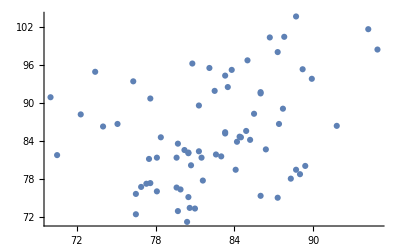

```mathematica
ListPlot[data[All,{"EntryWeight","ExitWeight"}]]
```

```mathematica
Correlation[
Normal@data[All,"EntryWeight"],
Normal@data[All,"ExitWeight"]
]
```

0.332406

```mathematica
data1=data[All,{"EntryWeight","ExitWeight"}];
```

```mathematica
Normal@data[All,"EntryWeight"];
```

```mathematica
QuantityMagnitude@Normal@data[All,{"EntryWeight","ExitWeight"}];
```

### this is the good thing

```mathematica
LinearModelFit[Values@QuantityMagnitude@Normal@data[All,{"EntryWeight","ExitWeight"}],x,x]
```

FittedModel[42.7006+0.51538 x]

```mathematica
linearModel=LinearModelFit[QuantityMagnitude@Normal@data[All,"EntryWeight"],QuantityMagnitude@Normal@data[All,"ExitWeight"],x]
```

LinearModelFit::dpbss: The number of unique basis functions is 71 fewer than the number of basis functions specified in {80.2,80.1,86.4,86.3,76.1,78.1,75.1,86.7,73.5,«33»,85.4,81.6,89.1,83.9,82.7,75.7,82.6,100.4,«22»}. Duplicated basis functions will be removed.

FittedModel[82.4083]